## 3 qubits

```mathematica
Needs["quantumJA`"]
```

```mathematica
diag=ArrayReshape[
Import["/home/deleonja/documents/component-erasing-maps/mathematica/data-alejo/"<>ToString[#]<>".dat"]
&/@Range[41],{41,64}];
```

```mathematica
choiMaps=(QC[#,3]//Reshuffle)&/@diag;
```

```mathematica
Min/@(Eigenvalues/@choiMaps//Chop)
```

{0.125,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

No hay eigenvalores negativos para ninguna de las 45 matrices de Choi asociadas a cada uno de los mapeos. Entonces los 41 son canales válidos!!!

```mathematica
#.#&/@diag
```

{1.,2.,4.,2.,4.,8.,4.,8.,16.,2.,4.,8.,4.,8.,16.,8.,16.,32.,4.,8.,16.,8.,16.,32.,16.,32.,64.,2.,4.,8.,4.,8.,16.,4.,8.,16.,8.,16.,32.,2.,4.}

```mathematica
diag[[3]]
```

{1.,1.,1.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ArrayReshape[diag[[15]],{4,4,4}]//MatrixForm
```

((1.
1.
1.
1.) | (1.
1.
1.
1.) | (0.
0.
0.
0.) | (0.
0.
0.
0.)
(1.
1.
1.
1.) | (1.
1.
1.
1.) | (0.
0.
0.
0.) | (0.
0.
0.
0.)
(0.
0.
0.
0.) | (0.
0.
0.
0.) | (0.
0.
0.
0.) | (0.
0.
0.
0.)
(0.
0.
0.
0.) | (0.
0.
0.
0.) | (0.
0.
0.
0.) | (0.
0.
0.
0.))

```mathematica
ArrayReshape[diag[[15]],{8,8}]//MatrixForm
```

(1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
ρPrueba=Table[If[Mod[i,2]≠0,1,0],{i,64}];
```

```mathematica
otra={{1,0,1,0},{0,1,0,1},{1,0,1,0},{0,1,0,1},{1,0,1,0},{0,1,0,1},{1,0,1,0},{0,1,0,1},{1,0,1,0},{0,1,0,1},{1,0,1,0},{0,1,0,1},{1,0,1,0},{0,1,0,1},{1,0,1,0},{0,1,0,1}};
```

```mathematica
MatrixForm/@ArrayReshape[otra,{4,4,4}]
```

{(1 | 0 | 1 | 0
0 | 1 | 0 | 1
1 | 0 | 1 | 0
0 | 1 | 0 | 1),(1 | 0 | 1 | 0
0 | 1 | 0 | 1
1 | 0 | 1 | 0
0 | 1 | 0 | 1),(1 | 0 | 1 | 0
0 | 1 | 0 | 1
1 | 0 | 1 | 0
0 | 1 | 0 | 1),(1 | 0 | 1 | 0
0 | 1 | 0 | 1
1 | 0 | 1 | 0
0 | 1 | 0 | 1)}

```mathematica
s=SparseArray[{1,6,11,16,18,21,41,61,64}->Append[ConstantArray[1,{8}],0]];
QC[s,3]//Reshuffle//Eigenvalues//Min
```

-1/4

```mathematica
MatrixForm/@ArrayReshape[s,{4,4,4}]
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0)}

```mathematica
QC[otra//Flatten,3]//Reshuffle//Eigenvalues//Min
```

0

```mathematica
QC[ρPrueba,3]//Reshuffle//Eigenvalues//Min
```

0

```mathematica
{{1,1,1,1},{0,0,0,0},{0,0,0,0},{1,1,1,1}}//MatrixForm
```

(1 | 1 | 1 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 1 | 1 | 1)

```mathematica
ρ=Pauli[{0,0}]+Pauli[{0,1}]+Pauli[{0,2}]+Pauli[{0,3}]+Pauli[{1,0}]+Pauli[{1,1}]+Pauli[{1,2}]+Pauli[{1,3}];
ρ=1/4*ρ;
ρ//MatrixForm
```

(1/2 | 1/4-ⅈ/4 | 1/2 | 1/4-ⅈ/4
1/4+ⅈ/4 | 0 | 1/4+ⅈ/4 | 0
1/2 | 1/4-ⅈ/4 | 1/2 | 1/4-ⅈ/4
1/4+ⅈ/4 | 0 | 1/4+ⅈ/4 | 0)

```mathematica
ρ==ConjugateTranspose[ρ]
```

True

```mathematica
Tr[ρ]
```

1

```mathematica
ρ//Eigenvalues//N
```

{1.36603,-0.366025,0.,0.}

```mathematica
Subsets[Range[4],{2}]
```

{{1,2},{1,3},{1,4},{2,3},{2,4},{3,4}}

```mathematica
indices=Subsets[Range[63]+1,{3}];
ρCB=SparseArray[Prepend[#,1]->ConstantArray[1,{4}],64]&/@indices;
```

```mathematica
validRhoCB={};
```

```mathematica
For[i=1,i≤1000,i++,
smallestEig=QC[ρCB[[i]],3]//Reshuffle//Eigenvalues//Min;
If[smallestEig≥0,
Append[validRhoCB,ρCB[[i]]];
]
]
```

```mathematica
validRhoCB//Length
```

0

```mathematica
MatrixPlot[#,ColorFunction->"Monochrome"]&/@ArrayReshape[ρCB[[4954]]//Normal,{4,4,4}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
prueba1=SparseArray[{{1,1,1},{1,2,1},{2,1,1},{2,2,1},{1,1,2},{1,2,2},{2,1,2},{2,2,2},
{3,3,3},{3,4,3},{4,4,3},{4,3,3},{3,3,4},{3,4,4},{4,4,4},{4,3,4},
{1,3,3},{1,3,4},{1,4,3},{1,4,4},{2,3,3},{2,3,4},{2,4,3},{2,4,4},
{3,1,1},{3,1,2},{3,2,1},{3,2,2},{4,1,1},{4,1,2},{4,2,1},{4,2,2}}->ConstantArray[1,{32}]]//Normal//Flatten;
```

```mathematica
MatrixPlot[#,ColorFunction->"Monochrome"]&/@ArrayReshape[prueba1,{4,4,4}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
QC[prueba1,3]//Reshuffle//Eigenvalues//Min
```

0

```mathematica
MatrixPlot[#,ColorFunction->"Monochrome"]&/@ArrayReshape[diag[[35]],{4,4,4}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Position[ArrayReshape[diag[[16]],{4,4,4}],1.]
```

{{1,1,1},{1,2,1},{1,3,1},{1,4,1},{2,1,1},{2,2,1},{2,3,1},{2,4,1}}

```mathematica
points={{0,0,0},{0,0,1},{1,1,0},{1,1,1}}
```

{{0,0,0},{0,0,1},{1,1,0},{1,1,1}}

```mathematica
Graphics3D[{Cube[#]&/@points},Axes->True,AxesLabel->{x,y,z},PlotRange->{{-0.5,3.5},{-0.5,3.5},{-0.5,3.5}}]
```

-Graphics3D-

```mathematica
diagElements=SparseArray[(points+1)->ConstantArray[1,{4}],{4,4,4}]//Normal//Flatten
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0}

```mathematica
QC[diagElements,3]//Reshuffle//Eigenvalues//Min
```

-1/4

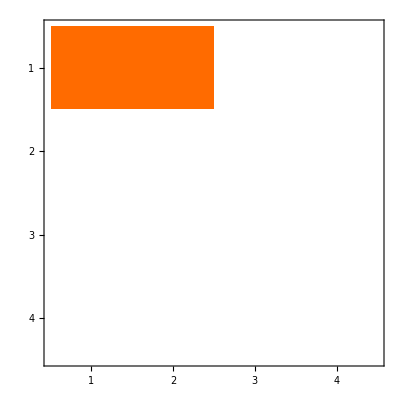
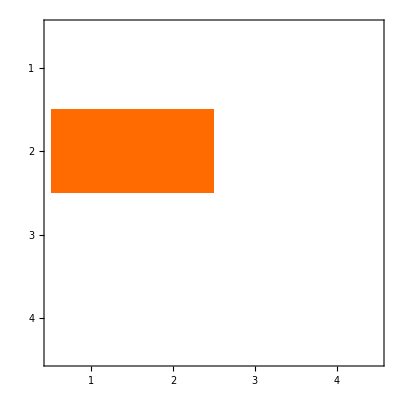
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot/@ArrayReshape[diag[[29]],{4,4,4}]
```

```mathematica
Inverse[{{1,0},{0,0}}]
```

Inverse::sing: Matrix {{1,0},{0,0}} is singular.

Inverse[{{1,0},{0,0}}]